```mathematica
Вариант 3;
```

Линейный сплайн, m = 1

```mathematica
Clear[P, PP, PPP, A, B, eq, koef, T, X, F, NN, n, xx, spl1, spl2, spl3];
1. Задаем начальные данные;
Subscript[x, 0] = 1; Subscript[x, 1] = 3; Subscript[x, 2] = 5; Subscript[x, 3] = 8;
Subscript[f, 0] = 4; Subscript[f, 1] = -20; Subscript[f, 2] = 45; Subscript[f, 3] = 76;
n = 3;
```

```mathematica
2. Формируем линейный интерполяционный сплайн;
Subscript[P, k_][t_] = Subscript[f, k] + (t - Subscript[x, k])*Subscript[A, k];
eq1 = Table[Subscript[P, k][Subscript[x, k + 1]] == Subscript[P, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
eq2 = {Subscript[P, n - 1][Subscript[x, n]] == Subscript[f, n]};
eq = Join[eq1, eq2]
koef = Solve[eq, {}]
spl1 = Table[Subscript[P, k][t] /. koef, {k, 0, n - 1}] // Expand // Flatten
Table[(spl1[[k]] /. t -> Subscript[x, k - 1]) == Subscript[f, k - 1], {k, 1, n}]
(spl1[[n]] /. t -> Subscript[x, n]) == Subscript[f, n]
```

{4+2 A_0==-20,-20+2 A_1==45,45+3 A_2==76}

{{A_0→-12,A_1→65/2,A_2→31/3}}

{16-12 t,-235/2+(65 t)/2,-20/3+(31 t)/3}

{True,True,True}

True

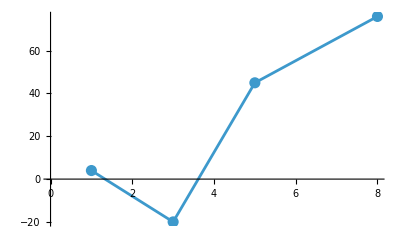

```mathematica
GrA = ListPlot[Table[{Subscript[x, i], Subscript[f, i]}, {i, 0, n}], PlotStyle -> {PointSize[0.02]}];
GrB = Table[Plot[spl1[[k]], {t, Subscript[x, k - 1], Subscript[x, k]}], {k, 1, n}];
Show[GrA, GrB]
```

Квадратичный сплайн, m = 2, S'(a) = 0

```mathematica
Clear[eq, eq1, eq2, eq3, eq4, koef];
Subscript[P, k_][t_] = Subscript[f, k] + (t - Subscript[x, k])*(Subscript[A, k]*t + Subscript[B, k]);
eq1 = Table[Subscript[P, k][Subscript[x, k + 1]] == Subscript[P, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
Subscript[PP, k_][t_] = D[Subscript[P, k][t], t];
eq2 = Table[Subscript[PP, k][Subscript[x, k + 1]] == Subscript[PP, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
eq3 = {Subscript[P, n - 1][Subscript[x, n]] == Subscript[f, n]};
eq4 = {Subscript[PP, 0][Subscript[x, 0]] == 0};
eq = Join[eq1, eq2, eq3, eq4]
koef = Solve[eq, {}]
spl2 = Table[Subscript[P, k][t] /. koef, {k, 0, n - 1}] // Expand // Flatten
Table[(spl2[[k]] /. t -> Subscript[x, k - 1]) == Subscript[f, k - 1], {k, 1, n}]
(spl2[[n]] /. t -> Subscript[x, n]) == Subscript[f, n]
(D[spl2[[1]], {t, 1}] /. t -> Subscript[x, 0]) == 0
```

{4+2 (3 A_0+B_0)==-20,-20+2 (5 A_1+B_1)==45,5 A_0+B_0==3 A_1+B_1,7 A_1+B_1==5 A_2+B_2,45+3 (8 A_2+B_2)==76,A_0+B_0==0}

{{A_0→-6,A_1→113/4,A_2→-236/9,B_0→6,B_1→-435/4,B_2→1981/9}}

{-2+12 t-6 t^2,1225/4-(387 t)/2+(113 t^2)/4,-9500/9+(3161 t)/9-(236 t^2)/9}

{True,True,True}

True

True

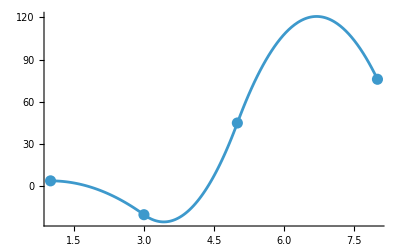

```mathematica
GrC = Table[Plot[spl2[[k]], {t, Subscript[x, k - 1], Subscript[x, k]}], {k, 1, n}];
Show[GrA, GrC, PlotRange -> All]
```

Кубический сплайн, m = 3, S'(a) = 0, S''(b) = 0

```mathematica
Clear[eq, eq1, eq2, eq3, eq4, eq5, eq6, koef];
a = Subscript[x, 0]; b = Subscript[x, n];
Subscript[P, k_][t_] = Subscript[f, k] + (t - Subscript[x, k])*(Subscript[A, k]*t^2 + Subscript[B, k]*t + Subscript[C, k]);
eq1 = Table[Subscript[P, k][Subscript[x, k + 1]] == Subscript[P, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
Subscript[PP, k_][t_] = D[Subscript[P, k][t], t];
eq2 = Table[Subscript[PP, k][Subscript[x, k + 1]] == Subscript[PP, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
Subscript[PPP, k_][t_] = D[Subscript[PP, k][t], t];
eq3 = Table[Subscript[PPP, k][Subscript[x, k + 1]] == Subscript[PPP, k + 1][Subscript[x, k + 1]], {k, 0, n - 2}];
eq4 = {Subscript[P, n - 1][Subscript[x, n]] == Subscript[f, n]};
eq5 = {Subscript[PP, 0][Subscript[x, 0]] == 0};
eq6 = {Subscript[PPP, n - 1][Subscript[x, n]] == 0};
eq = Join[eq1, eq2, eq3, eq4, eq5, eq6]
koef = Solve[eq, {}]
spl3 = Table[Subscript[P, k][t] /. koef, {k, 0, n - 1}] // Expand // Flatten
Table[(spl3[[k]] /. t -> Subscript[x, k - 1]) == Subscript[f, k - 1], {k, 1, n}]
(spl3[[n]] /. t -> Subscript[x, n]) == Subscript[f, n]
(D[spl3[[1]], {t, 1}] /. t -> a) == 0
(D[spl3[[n]], {t, 2}] /. t -> b) == 0
```

{4+2 (9 A_0+3 B_0+C_0)==-20,-20+2 (25 A_1+5 B_1+C_1)==45,9 A_0+3 B_0+2 (6 A_0+B_0)+C_0==9 A_1+3 B_1+C_1,25 A_1+5 B_1+2 (10 A_1+B_1)+C_1==25 A_2+5 B_2+C_2,16 A_0+2 B_0==12 A_1+2 B_1,24 A_1+2 B_1==20 A_2+2 B_2,45+3 (64 A_2+8 B_2+C_2)==76,A_0+B_0+C_0==0,38 A_2+2 B_2==0}

{{A_0→511/66,A_1→-537/88,A_2→1537/1188,B_0→-1220/33,B_1→739/12,B_2→-29203/1188,C_0→643/22,C_1→-32435/264,C_2→3353/27}}

{-555/22+(4369 t)/66-(2951 t^2)/66+(511 t^3)/66,30675/88-(81209 t)/264+(21091 t^2)/264-(537 t^3)/88,-15550/27+(97849 t)/396-(3074 t^2)/99+(1537 t^3)/1188}

{True,True,True}

True

True

True

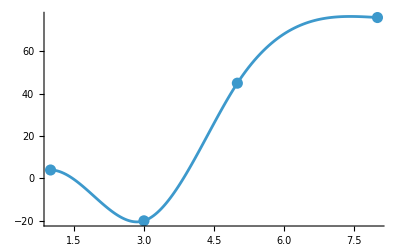

```mathematica
GrD = Table[Plot[spl3[[k]], {t, Subscript[x, k - 1], Subscript[x, k]}], {k, 1, n}];
Show[GrA, GrD, PlotRange -> All]
```

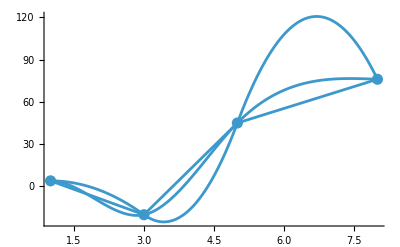

```mathematica
Все сплайны в одной системе координат;
Show[GrA, GrB, GrC, GrD, PlotRange -> All]
```